## Homework 5

## Exercise 1

(-a_r | 0
-l_(Π+r) | 1) (dr
dm) =(a_f df-dy
l_(Π+r)dΠ+l_y dy)

b^-1== (-1/a_r | 0
-(l_(r+Π))/a_r | 1)
(dr
dm) == (-1/a_r | 0
-(l_(r+Π))/a_r | 1) (a_f df-dy
l_(Π+r)dΠ+l_y dy)
(dr
dm) == ((dy-df a_f)/a_r
dy l_y+((dy-df a_f+dΠ a_r) l_(r+Π))/a_r)
We can  find  dr/df by dividing the first row of the matrix by df

## Exercise 2

Maximize x y s.t. p_x x + p_y y = 100
ℒ = x y + λ (p_x x + p_y y - 100)
(∂ℒ)/(∂x) = y + λ p_x = 0
(∂ℒ)/(∂y) = x + λ p_y = 0 
(∂ℒ)/(∂λ) = p_x x + p_y y - 100 = 0

```mathematica
l = x y + λ(px x + py y - 100)
lx = D[l, x] == 0
ly = D[l, y] == 0
ll = D[l, λ] == 0
soln = Solve[{lx, ly, ll}, {x, y, λ}]
```

x y+(-100+px x+py y) λ

y+px λ==0

x+py λ==0

-100+px x+py y==0

{{x→50/px,y→50/py,λ→-50/(px py)}}

## Computational Exercise 1

1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1Original Relation

-Graphics-

1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1Symmetric Subelation

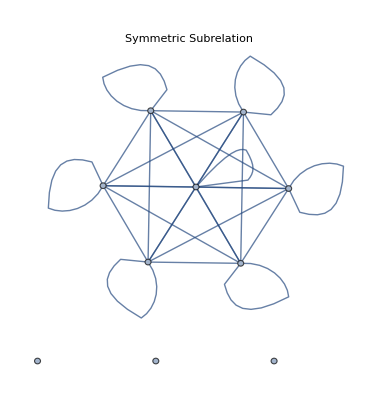

```mathematica
ClearAll[result]
subsym[x_] := Module[{result=Table[Table[0, Length[x]], Length[x]]},
Do[If[x[[i]][[j]] == 1 && x[[j]][[i]] == 1,
result[[i]][[j]] = 1,
0], {i, 1, Length[x]}, {j, 1, Length[x]}];
result
]
x = Table[{1,0,1,1,0,1,1,1,0,1}, 10];
x//Labeled[TableForm[#],"Original Relation"]&
AdjacencyGraph[x, PlotLabel->"Graph of original adjacency matrix"]
s = subsym[x];
s//Labeled[TableForm[#],"Symmetric Subelation"]&
AdjacencyGraph[s, PlotLabel->"Symmetric Subrelation"]
```

## Compuational Exercise 2

```mathematica
adjMatrix = Table[RandomChoice[{0, 1},5], 5]
adjMatrix//Labeled["Adjacency Matrix", TableForm[#]]&
adjGraph = AdjacencyGraph[adjMatrix, PlotLabel->"Adjacency Graph"]
```

{{1,0,1,1,0},{1,1,1,1,0},{0,0,0,1,1},{1,1,1,1,0},{0,0,1,0,0}}

Adjacency Matrix1 | 0 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0

-Graphics-

```mathematica
StringForm["Is the relation reflexive? ``", AllTrue[Diagonal[adjMatrix], # == 1 &]]
symmetric[x_] := Module[{},
Do[
If
[x[[i]][[j]] == 1 && x[[j]][[i]]  == 0 ,
Return[False]
];
Return[True], 
{i, 1, Length[x]}, 
{j, 1, Length[x]}
]
]
StringForm["Is the relation symmetric? ``", symmetric[adjMatrix]]
```

Is the relation reflexive? False

Is the relation symmetric? True

```mathematica
reflexivize[x_]:= Module[{result = x}, 
Do[
result[[i]][[i]]=1, 
{i, 1, Length[x]}];
Return[result]]
reflexiveAdjMatrix = reflexivize[adjMatrix];
StringForm["Is the new relation (with reflexive closure) reflexive? ``", AllTrue[Diagonal[reflexiveAdjMatrix], # == 1 &]]
AdjacencyGraph[reflexiveAdjMatrix]
```

Is the new relation (with reflexive closure) reflexive? True

-Graphics-

Is the new relation (with symmtric closure)? True

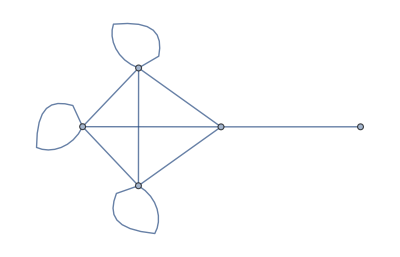

```mathematica
symmetrize[x_]:=Module[{result=x}, Do[
If[result[[i]][[j]] == 1, result[[j]][[i]] =1, ],
{i, 1, Length[result]}, {j, 1, Length[result]}];
Return[result]]
symmetricAdjMatrix = symmetrize[adjMatrix] ;
StringForm["Is the new relation (with symmtric closure)? ``", symmetric[symmetricAdjMatrix]]
AdjacencyGraph[symmetricAdjMatrix]
```

## Computational Exercise 3

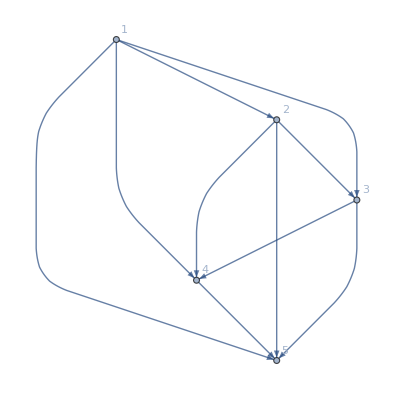

SparseArray[<10>, {5, 5}]

< | 1 | 2 | 3 | 4 | 5
1 | 0 | 1 | 1 | 1 | 1
2 | 0 | 0 | 1 | 1 | 1
3 | 0 | 0 | 0 | 1 | 1
4 | 0 | 0 | 0 | 0 | 1
5 | 0 | 0 | 0 | 0 | 0

```mathematica
g = RelationGraph[Less,Range[1, 5]]
a = AdjacencyMatrix[g]
a//Labeled["<", TableForm[#, TableHeadings->{{1, 2, 3, 4, 5}, {1, 2, 3, 4, 5}}]]&
```

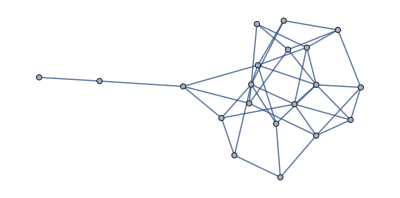

```mathematica
g0 = RandomGraph[BernoulliGraphDistribution[20,0.2]]
```

```mathematica
d = VertexDegree[g0]
```

{3,4,5,4,8,6,7,6,4,4,4,3,5,4,4,3,1,2,4,3}

```mathematica
Tally[d]
```

{{3,4},{4,8},{5,2},{8,1},{6,2},{7,1},{1,1},{2,1}}

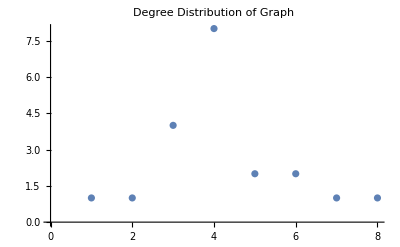

```mathematica
ListPlot[Tally[d], PlotLabel->"Degree Distribution of Graph"]
```

## Computational Exercise 4

```mathematica
adjList = {1->1, 1->3, 2->1, 2->2, 2->3, 3->2,3->3, 3->5, 4->1,4->2,4->3, 4->4, 5->1,5->2,5->3,5->5}
g1 = Graph[adjList]
AdjacencyMatrix[g1]//MatrixForm
```

{1->1,1->3,2->1,2->2,2->3,3->2,3->3,3->5,4->1,4->2,4->3,4->4,5->1,5->2,5->3,5->5}

-Graphics-

(1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1)